```mathematica
(****************************)
(***** Updated Profiles *****)
(*********** ISO ************)
(****************************)
G=7 10^-20(1/(3.086 10^16))^3((2 10^30)/1);(*Newton's constant in kpc^3/(msol s^2)*)
VmaxDracoIso=10^1.343(1/(3.086 10^16)); (* kpc/s *)
RmaxDracoIso=10^0.0266; (* kpc *)
v0Draco=0.630 VmaxDracoIso;
rho0Draco=(2.556 VmaxDracoIso^2)/(G RmaxDracoIso^2);
a0Draco=(4π G)/v0Draco^2 rho0Draco;
solDraco=NDSolve[{f''[y]+2/y f'[y]+a0Draco/(1-y)^4 ⅇ^f[y]==0,f[10^-10]==0,f'[10^-10]==0 },f,{y,10^-10,4000},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->Infinity,Method->"StiffnessSwitching"];
```

NDSolve::precw: The precision of the differential equation ({{(71.5961 ⅇ^f[y])/(1+Times[«2»])^4+(2 f'[y])/y+f''[y]==0,f[1/10000000000]==0,f'[1/10000000000]==0},{},{},{},{}}) is less than WorkingPrecision (60.).

NDSolve::ndsz: At y == 0.999999999999999999999999999999999999999999999999999999190187, step size is effectively zero; singularity or stiff system suspected.

```mathematica
ISOdataDraco=Table[{10^i,Extract[(rho0Draco ⅇ^f[10^i/(1+10^i)]/.solDraco),1]},{i,-10+Log[10,1.2],Log[10,4000],(Log[10,4000]-(-10+Log[10,1.2]))/100}];
ISODraco=Interpolation[ISOdataDraco,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
(************************)
(********* NFW **********)
(************************)
VmaxDraco=10^1.434(1/(3.086 10^16));(* kpc/s *)
RmaxDraco=10^0.6230; (* kpc *)
rhosDraco=(1.721 VmaxDraco^2)/(G RmaxDraco^2)
rsDraco=0.462RmaxDraco
NFWDraco[r_]:=rhosDraco/(r/rsDraco(1+r/rsDraco)^2);
```

1.58873×10^7

1.93929

```mathematica
(***********************)
(********* CUT *********)
(***********************)
rTidalDraco=10^1.019;(* kpc *)
CUTDraco[r_]=NFWDraco[rTidalDraco](rTidalDraco/r)^5;
rTidalDracoIso=10^1.319;(* kpc *)
CUTDracoIso[r_]=ISODraco[rTidalDracoIso](rTidalDracoIso/r)^5;
```

```mathematica
(***********************************)
(********* Draco Modeling **********)
(***********************************)
π 10^7 (* s/yr *);
3 10^19(* m / kpc *);
2 10^33(* g / msol *);
2 10^30(* kg / msol *);
1.8 10^-27(* kg / GeV *);
DracoBoundRadius10e5=      0.2(0.033);(* kpc *)
ISODracoBoundRadius10e5= 0.2(0.04661958) (* kpc *)
DracoannRadius0=  1.1 10^-11(* kpc *);
DracoannRadius10e5=   8.24 10^-7(* kpc *);
ISODracoannRadius10e5= 1.82 10^-9(* kpc *);
```

0.00932392

```mathematica
4 π Integrate[r^2 NFWDraco[r],{r,0,0.00023}]
```

10.239

```mathematica
.00023 0.2
```

0.000046

```mathematica
V0Draco=13.88/(3 10^16);(* kpc / s *)
rspikeDracoalt[z_]:=(G z)/V0Draco^2;(* kpc *)
```

```mathematica
V0Draco ((3.086 10^16)/1)
```

14.2779

```mathematica
rspikeDracoalt[10^5]
```

0.00222538

```mathematica
NFWDraco[0.0066]
```

4.63656×10^9

```mathematica
ISODraco[0.0022]
```

2.41882×10^8

```mathematica
rspikeDraco
```

rspikeDraco

```mathematica
(*******************)
(*** Draco Spike ***)
(*******************)
DracoSpike10e5[r_]:=NFWDraco[DracoBoundRadius10e5](DracoBoundRadius10e5/r)^(7/3);
ISODracoSpike10e5[r_]:=ISODraco[ISODracoBoundRadius10e5](ISODracoBoundRadius10e5/r)^(3/2);
DracoSpikealt[r_,z_]:=ISODraco[rspikeDracoalt[z]](rspikeDracoalt[z]/r)^(7/4);
```

```mathematica
ProfileDraco0[r_]:=Piecewise[{{NFWDraco[DracoannRadius0],r<DracoannRadius0},{NFWDraco[r],DracoannRadius0≤ r≤rTidalDraco },{CUTDraco[r],rTidalDraco<r}}];
ProfileDraco10e5[r_]:=Piecewise[{{0,r<DracoannRadius10e5},{DracoSpike10e5[r],DracoannRadius10e5≤ r≤DracoBoundRadius10e5},{NFWDraco[r],DracoBoundRadius10e5<r≤rTidalDraco },{CUTDraco[r],rTidalDraco<r}}];
```

```mathematica
ISOProfileDraco0[r_]:=Piecewise[{{ISODraco[r],0<r≤rTidalDracoIso },{CUTDracoIso[r],rTidalDracoIso<r}}];
ISOProfileDraco10e5[r_]:=Piecewise[{{0,r< ISODracoannRadius10e5},{ISODracoSpike10e5[r],ISODracoannRadius10e5≤ r≤ISODracoBoundRadius10e5 },{ISODraco[r],ISODracoBoundRadius10e5<r≤rTidalDracoIso },{CUTDracoIso[r],rTidalDracoIso<r}}];
ISOProfileDracoalt[r_,z_]:=Piecewise[{{0,r< ISODracoannRadius10e5},{DracoSpikealt[r,z],ISODracoannRadius10e5≤ r≤rspikeDracoalt[z]},{ISODraco[r],rspikeDracoalt[z]<r≤rTidalDracoIso },{CUTDracoIso[r],rTidalDracoIso<r}}];
```

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.00182]}},{i,min10,max10,1}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.00181]}},{i,min10,max10},{k,9}],1]]];
```

```mathematica
tPowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

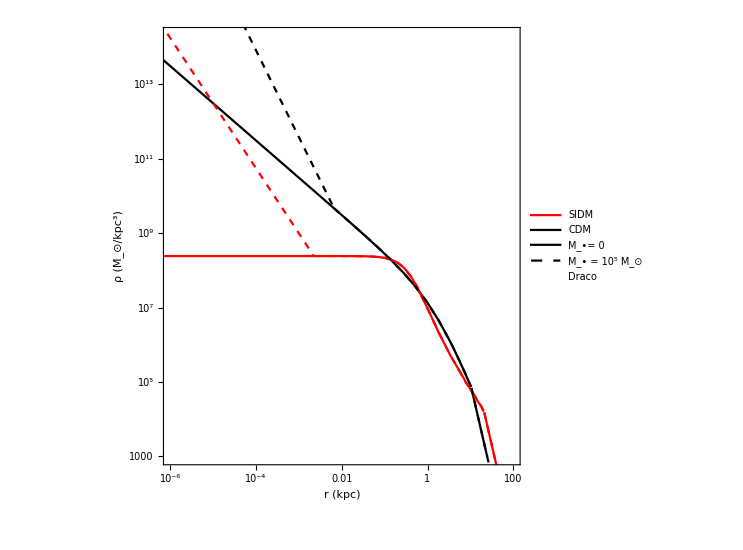

```mathematica
Show[LogLogPlot[ProfileDraco0[r],{r,10^-10,4000},PlotStyle->{Black},PlotRange->{{10^-6,10^2},{ 10^3,2 10^14}},PlotLegends-> Placed[LineLegend[{Red,Black},{"SIDM","CDM"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.85,0.85}],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],LogLogPlot[ISOProfileDraco0[r],{r,10^-10,4000},PlotStyle->Red],LogLogPlot[ISOProfileDracoalt[r,10^5],{r,10^-10,4000},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{Black,{Black,Dashed}},{Row[{Subscript[Style["M",Italic],"•"] ,"= 0"}],Row[{Subscript[Style["M",Italic],"•"]," = 10^5 M_⊙"}]},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.2,0.1}]],LogLogPlot[ProfileDraco10e5[r],{r,10^-10,4000},PlotStyle->{Black,Dashed}],LogLogPlot[1,{x,10,10000},PlotStyle->{White},PlotLegends-> Placed[LineLegend[{White},{"Draco"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.5,0.93}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.003],Black],FrameLabel-> {Row[{Text[Style["r",Italic]]," (kpc)"}],Row[{"ρ (",Subscript["M","⊙"],"/kpc^3)"}]},LabelStyle->Directive[Black,FontSize-> 25],AspectRatio-> 1]
```

```mathematica
ProfileDraco0[  1.1 10^-11]
```

2.8009×10^18

```mathematica
(*********************************)
(**** Draco / Fornac J Factor ****)
(*********************************)
Dist=76;(* kpc *)
r[θ_,s_]:=√(Dist^2+s^2-2Dist s Cos[θ]);
ρDraco0 [θ_,s_]=ProfileDraco0[r[θ,s]]; 
ρDracoISO0 [θ_,s_]=ISOProfileDraco0[r[θ,s]];  
θMax=π/180(0.5);
Off[NIntegrate::inumr]
funcDraco0[θ_]=NIntegrate[ρDraco0[θ,s]^2,{s,Dist-15,Dist+15},MaxRecursion->10];  
funcDracoISO0[θ_]=NIntegrate[ρDracoISO0[θ,s]^2,{s,Dist-15,Dist+15}];
```

```mathematica
JDraco=2π NIntegrate[Sin[θ]funcDraco0[θ],{θ,0,θMax},MaxRecursion->25]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 25 recursive bisections in θ near {θ} = {1.05377×10^-8}. NIntegrate obtained 1.51768×10^11 and 636108. for the integral and error estimates.

9.53584×10^11

```mathematica
JDracoISO=2π NIntegrate[Sin[θ]funcDracoISO0[θ],{θ,0,θMax}]
```

9.94158×10^11

```mathematica
DracoJFactor=JDraco (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

4.79156×10^18

```mathematica
ISODracoJfactor=JDracoISO (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

4.99544×10^18

```mathematica
(*********************************)
(****** Flux Upper Limit *********)
(*********************************)
fluxdata={{6.7876,7.6530 10^-10},
{8.6395,6.9424 10^-10},
{10.997,6.1664 10^-10},
{13.997,5.5011 10^-10},
{17.816,4.8460 10^-10},
{22.677,4.2123 10^-10},
{28.864,3.6158 10^-10},
{36.739,3.1113 10^-10},
{46.763,2.6795 10^-10},
{59.522,2.2197 10^-10},
{75.762,1.8838 10^-10},
{96.434,1.6071 10^-10},
{122.74,1.3710 10^-10},
{156.23,1.1674 10^-10},
{198.86,1.0249 10^-10},
{253.12,9.1609 10^-11},
{322.18,8.1695 10^-11},
{410.08,7.4340 10^-11},
{521.97,6.9442 10^-11},
{664.39,6.4797 10^-11},
{845.66,6.0553 10^-11},
{979.47,5.8721 10^-11},
{1000, 5.84 10^-11}};
flux=Interpolation[fluxdata];
```

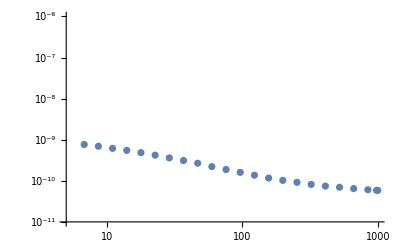

```mathematica
ListLogLogPlot[fluxdata,PlotRange->{{5,1000},{10^-11,10^-6}}]
```

```mathematica
(***********************)
(**** bbbar Spectra ****)
(***********************)
xidata={{10,  9.99463},
{20, 14.0186},
{40, 18.6323},
{70, 23.015},
{100, 26.2174},
{200, 33.6505},
{400,43.0486},
{700, 52.2291},
{1000,  58.8666}};
xi=Interpolation[xidata,InterpolationOrder->3];
```

```mathematica
step=(Log10[1000]-Log10[10])/10;
stepin= Table[10^x,{x,Log10[10],Log10[1000],step}]
```

{10,10 10^(1/5),10 10^(2/5),10 10^(3/5),10 10^(4/5),100,100 10^(1/5),100 10^(2/5),100 10^(3/5),100 10^(4/5),1000}

```mathematica
(*****************)
(** NFW γ > 3/2 **)
(*****************)
```

```mathematica
(*[x]=GeV*)
Mbh=10^5(* Msol *); 
T=10 10^9(* yr *)((365(* day/yr*))/1)((24(* hr/day *))/1)((60 (* min/hr *))/1)((60(* s/min *))/1); (* s *)
alpha[x_]:=1/(8π)(xi[x]DracoJFactor(* GeV^2/cm^5 *))/x^2; (* cm^-5 *)
gamma=7/3;
betagamma[x_,z_,γ_]:=((0.2)^(3(1-1/γ))xi[x])/(2(2 γ -3)π^(3/2(1-1/γ)))(((((rhosDraco(* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3)) (rsDraco(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *))))^(3/2(3/γ-1))(z(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))^(3/2(1-1/γ)))/(T^(2-3/γ)(Dist(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *)) )^2 x^(3/γ)));  (* cm^-20/7 s^-5/7 *)
```

```mathematica
limitDraco[i_,j_,k_]:=NSolve[  alpha[i] y+ betagamma[i,j,k] y^(3/k -1)==flux[i],y,Reals][[1]];
```

```mathematica
DracoXsectData10e5= Table[{i,y/.limitDraco[i,Mbh,7/3] } ,{i,stepin}]
DracoXsect10e5=Interpolation[DracoXsectData10e5]
```

{{10,1.29039×10^-35},{10 10^(1/5),2.10439×10^-35},{10 10^(2/5),3.07557×10^-35},{10 10^(3/5),4.75759×10^-35},{10 10^(4/5),6.40854×10^-35},{100,9.77968×10^-35},{100 10^(1/5),1.55482×10^-34},{100 10^(2/5),3.0724×10^-34},{100 10^(3/5),6.61449×10^-34},{100 10^(4/5),1.87499×10^-33},{1000,5.74125×10^-33}}

InterpolatingFunction[…]

```mathematica
(*****************)
(** NFW γ = 3/2 **)
(*****************)
```

```mathematica
alpha[x_]:=1/(8π)(xi[x]DracoJFactor(* GeV^2/cm^5 *))/x^2; (* cm^-5 *)
betastarr[x_,z_]:=0.2/3(xi[x](z/π(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))^(1/2) (* GeV *))/(x^2(Dist(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *)))^2) (((rhosDraco(* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3)) (rsDraco(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *))))^(3/2);  
gammastarr[x_,z_]:=0.2 x (z/π(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))^(1/2)/( (((rhosDraco(* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *))))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3)) (rsDraco(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *))))^(3/2) T);
```

```mathematica
limitDracostarr[i_,j_] :=NSolve[  alpha[i] y- betastarr[i,j] y Log[y/gammastarr[i,j]]==flux[i],y][[1]] ;
```

```mathematica
(*****************)
(** NFW Mbh = 0 **)
(*****************)
```

```mathematica
limitDraco0[i_]:=NSolve[  alpha[i] y==flux[i],y,Reals][[1]];
```

```mathematica
DracoXsectData0= Table[{i,y/.limitDraco0[i] } ,{i,stepin}]
DracoXsect0=Interpolation[DracoXsectData0]
```

{{10,3.3969×10^-26},{10 10^(1/5),5.42783×10^-26},{10 10^(2/5),8.4056×10^-26},{10 10^(3/5),1.32299×10^-25},{10 10^(4/5),2.00161×10^-25},{100,3.13822×10^-25},{100 10^(1/5),4.97817×10^-25},{100 10^(2/5),8.40313×10^-25},{100 10^(3/5),1.4536×10^-24},{100 10^(4/5),2.72013×10^-24},{1000,5.20363×10^-24}}

InterpolatingFunction[…]

```mathematica
(*****************)
(** ISO γ > 3/2 **)
(*****************)
```

```mathematica
(*[x]=GeV*)
Mbh=10^5(* Msol *); 
T=10 10^9(* yr *)((365(* day/yr*))/1)((24(* hr/day *))/1)((60 (* min/hr *))/1)((60(* s/min *))/1); (* s *)
ISOalpha[x_]:=1/(8π)(xi[x]ISODracoJfactor(* GeV^2/cm^5 *))/x^2; (* cm^-5 *)
ISObetastarr[x_,z_,γ_]:=(3(0.2)^3 xi[x] (z(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))))/(4π x^(3/γ)T^(2/7)(ISOProfileDraco0[10^-8](* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3))^(9/7)(Dist(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *)))^2);  (* cm^-20/7 s^-5/7 *)
```

```mathematica
limitISODracostarr[i_,j_,k_]:=NSolve[  ISOalpha[i] y+ ISObetastarr[i,j,k] y^((3-k)/k)==flux[i],y,Reals][[1]] ;
```

```mathematica
(*****************)
(** ISO γ > 3/2 **)
(****** V2 *******)
(*****************)
(*[x]=GeV*)
Mbh=10^5(* Msol *); 
G=7 10^-20(1/(3.086 10^16))^3((2 10^30)/1);(*Newton's constant in kpc^3/(msol s^2)*)
clight=2.998 10^5(1/(3 10^16)) ; (* kpc /s *)
T=10 10^9(* yr *)((365(* day/yr*))/1)((24(* hr/day *))/1)((60 (* min/hr *))/1)((60(* s/min *))/1); (* s *)
rschDraco[z_]:=(2 G z)/clight^2; (* kpc *)
rbhDraco[z_]:=NSolve[4π Integrate[r^2 ISOProfileDraco0[10^-3],{r,0,y},GenerateConditions->False]==2z,y,Reals][[1]][[1]];
rspikeDraco[z_]:=0.2 y/.rbhDraco[z]
QDracostar[γ_,z_]:=(ISOProfileDraco0[rspikeDraco[z]]^2 rspikeDraco[z]^(2γ))/((2γ-3)(2 rschDraco[z])^(2γ-3));   
QDracostaralt[γ_,z_]:=(ISOProfileDraco0[rspikeDracoalt[z]]^2 rspikeDracoalt[z]^(2γ))/((2γ-3)(2rschDraco[z])^(2γ-3)) ;     
ISOalphaV2star[x_]:=1/2 xi[x]/(4π x^2)ISODracoJfactor(* GeV^2/cm^5 *); (* cm^-5 *)
ISObetaV2star[x_,z_,γ_]:=1/2 xi[x]/(4π x^2)(4π)/Dist^2 QDracostar[γ,z](* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2;  (* cm^-5 *) 
ISObetaV2staralt[x_,z_,γ_]:=1/2 xi[x]/(4π x^2)(4π)/Dist^2 QDracostaralt[γ,z](* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2;  (* cm^-5 *)
```

```mathematica
limitDracoV2star[x_,z_,γ_] :=NSolve[ ( ISOalphaV2star[x] +ISObetaV2star[x,z,γ]) y ==flux[x],y][[1]]
```

```mathematica
ISODracoXsectData= Table[{x,y/.limitDracoV2star[x,Mbh,7/4][[1]]} ,{x,stepin}]
ISODracoXsect=Interpolation[ISODracoXsectData]
```

{{10,2.97332×10^-27},{10 10^(1/5),4.751×10^-27},{10 10^(2/5),7.35746×10^-27},{10 10^(3/5),1.15802×10^-26},{10 10^(4/5),1.75201×10^-26},{100,2.74689×10^-26},{100 10^(1/5),4.35741×10^-26},{100 10^(2/5),7.35529×10^-26},{100 10^(3/5),1.27235×10^-25},{100 10^(4/5),2.38094×10^-25},{1000,4.55476×10^-25}}

InterpolatingFunction[…]

```mathematica
limitDracoV2staralt[x_,z_,γ_] :=NSolve[ ( ISOalphaV2star[x] +ISObetaV2staralt[x,z,γ]) y ==flux[x],y][[1]]
```

```mathematica
ISODracoXsectDataalt= Table[{x,y/.limitDracoV2staralt[x,Mbh,7/4][[1]]} ,{x,stepin}]
ISODracoXsectalt=Interpolation[ISODracoXsectDataalt]
```

{{10,3.16189×10^-26},{10 10^(1/5),5.05233×10^-26},{10 10^(2/5),7.82409×10^-26},{10 10^(3/5),1.23147×10^-25},{10 10^(4/5),1.86313×10^-25},{100,2.92111×10^-25},{100 10^(1/5),4.63377×10^-25},{100 10^(2/5),7.82179×10^-25},{100 10^(3/5),1.35304×10^-24},{100 10^(4/5),2.53195×10^-24},{1000,4.84364×10^-24}}

InterpolatingFunction[…]

```mathematica
(*****************)
(** ISO γ = 3/2 **)
(*****************)
```

```mathematica
ISOalpha[x_]:=1/2(xi[x] ISODracoJfactor(* GeV^2/cm^5 *))/(4π x^2); 
ISObeta[x_,z_]:=0.2^3/(2π)(xi[x](z(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))) (* GeV *))/(x^2(Dist(* kpc *)(3 10^19(* m / kpc *) )(100 (* cm /m *)))^2) (ISOProfileDraco0[10^-8](* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3));  
ISOgamma[x_]:=x/((ISOProfileDraco0[10^-8](* msol / kpc^3 *)(1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))/((3 10^19(* m / kpc *) )^3(100 (* cm /m *))^3)) T);
```

```mathematica
limitISODraco[i_,j_]:=NSolve[  ISOalpha[i] y- ISObeta[i,j] y Log[y/ISOgamma[i]]==flux[i],y];
```

```mathematica
ISODracoXsectData10e5= Table[{i,y/.limitISODraco[i,Mbh][[1]]} ,{i,stepin}]
ISODracoXsect10e5=Interpolation[ISODracoXsectData10e5]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

{{10,3.2502×10^-26},{10 10^(1/5),5.19343×10^-26},{10 10^(2/5),8.04258×10^-26},{10 10^(3/5),1.26586×10^-25},{10 10^(4/5),1.91515×10^-25},{100,3.00266×10^-25},{100 10^(1/5),4.76313×10^-25},{100 10^(2/5),8.04022×10^-25},{100 10^(3/5),1.39084×10^-24},{100 10^(4/5),2.60274×10^-24},{1000,4.97919×10^-24}}

InterpolatingFunction[…]

```mathematica
(*****************)
(** ISO γ = 3/2 **)
(****** V2 *******)
(*****************)
ISOalphaV2[x_]:=1/2 xi[x]/(4π x^2)ISODracoJfactor(* GeV^2/cm^5 *); (* cm^-5 *)
QDraco[z_]:=ISOProfileDraco0[rspikeDraco[z]]^2 rspikeDraco[z]^3 Log[rspikeDraco[z]/(2rschDraco[z])];   
QDracoalt[z_]:=ISOProfileDraco0[rspikeDracoalt[z]]^2 rspikeDracoalt[z]^3 Log[rspikeDracoalt[z]/(2rschDraco[z])];   
ISObetaV2[x_,z_]:=1/2 xi[x]/(4π x^2)(4π)/Dist^2 QDraco[z](* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
ISObetaV2alt[x_,z_]:=1/2 xi[x]/(4π x^2)(4π)/Dist^2 QDracoalt[z](* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
```

```mathematica
limitISODracoV2[x_,z_]:=NSolve[  (ISOalphaV2[x]+ISObetaV2[x,z])y==flux[x],y];
```

```mathematica
limitISODracoV2alt[x_,z_]:=NSolve[  (ISOalphaV2[x]+ISObetaV2alt[x,z])y==flux[x],y];
```

```mathematica
(*****************)
(** ISO Mbh = 0 **)
(*****************)
```

```mathematica
limitISODraco0[i_]:=NSolve[  ISOalpha[i] y==flux[i],y];
```

```mathematica
ISODracoXsectData0= Table[{i,y/.limitISODraco0[i][[1]]} ,{i,stepin}]
ISODracoXsect0=Interpolation[ISODracoXsectData0]
```

{{10,3.25826×10^-26},{10 10^(1/5),5.20631×10^-26},{10 10^(2/5),8.06255×10^-26},{10 10^(3/5),1.269×10^-25},{10 10^(4/5),1.91992×10^-25},{100,3.01014×10^-25},{100 10^(1/5),4.775×10^-25},{100 10^(2/5),8.06018×10^-25},{100 10^(3/5),1.39428×10^-24},{100 10^(4/5),2.60912×10^-24},{1000,4.99126×10^-24}}

InterpolatingFunction[…]

```mathematica
PowerTicks2[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.001]}},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]];
```

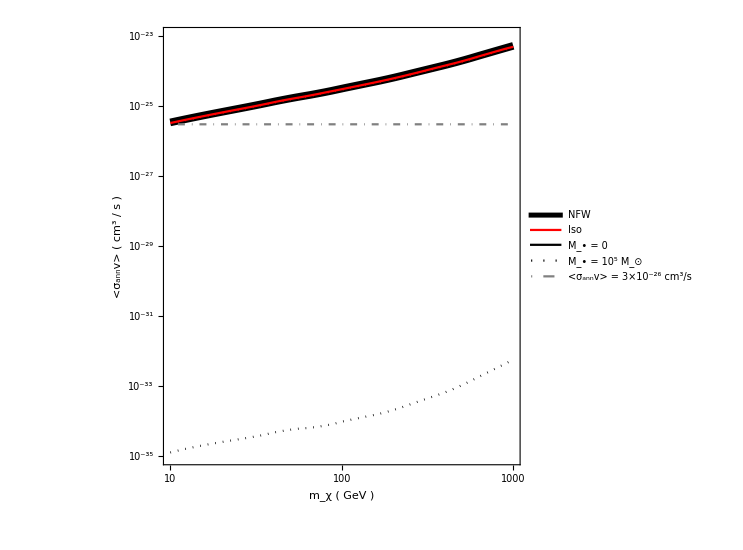

```mathematica
Show[LogLogPlot[DracoXsect0[x],{x,10,1000},PlotStyle->{Black,Thickness[0.01]},PlotRange->{{10,1000},{10^-35, 10^-23}},PlotLegends-> Placed[LineLegend[{{Black,Thickness[0.01]},Red},{"NFW","Iso"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.8,0.5}],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],LogLogPlot[DracoXsect10e5[x],{x,10,1000},PlotStyle->{Black,Dotted},PlotLegends-> Placed[LineLegend[{Black,Dotted,{Gray,DotDashed}},{"M_• = 0 ","M_• = 10^5 M_⊙","<σ_annv> = 3×10^-26 cm^3/s"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.3,0.5}]],LogLogPlot[ISODracoXsect0[x],{x,10,1000},PlotStyle->{Red}],LogLogPlot[ISODracoXsectalt[x],{x,10,1000},PlotStyle->{Red,Dotted}],LogLogPlot[3 10^-26,{x,10,1000},PlotStyle->{Gray,DotDashed}],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"m_χ ( GeV )","<σ_annv> ( cm^3 / s )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

```mathematica
stepbh=(Log10[10^15]-Log10[10^-1])/100;
stepbhin= Table[10^x,{x,Log10[10^-1],Log10[10^15],stepbh}];
```

```mathematica
ISODracoXsectData10= Table[{i,y/.limitISODraco[10,i][[1]]} ,{i,stepbhin}];
ISODracoXsect10=Interpolation[ISODracoXsectData10];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

```mathematica
ISODracoXsectData10V2= Table[{i,y/.limitDracoV2star[10,i,7/4][[1]]} ,{i,stepbhin}];
ISODracoXsect10V2=Interpolation[ISODracoXsectData10V2];
```

```mathematica
ISODracoXsectData10V2alt= Table[{i,y/.limitDracoV2staralt[10,i,7/4][[1]]} ,{i,stepbhin}];
ISODracoXsect10V2alt=Interpolation[ISODracoXsectData10V2alt];
```

```mathematica
ISODracoXsectData1000= Table[{i,y/.limitISODraco[1000,i][[1]]} ,{i,stepbhin}];
ISODracoXsect1000=Interpolation[ISODracoXsectData1000];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

```mathematica
ISODracoXsectData1000V2= Table[{i,y/.limitDracoV2star[1000,i,7/4][[1]]} ,{i,stepbhin}];
ISODracoXsect1000V2=Interpolation[ISODracoXsectData1000V2];
```

```mathematica
ISODracoXsectData1000V2alt= Table[{i,y/.limitDracoV2staralt[1000,i,7/4][[1]]} ,{i,stepbhin}];
ISODracoXsect1000V2alt=Interpolation[ISODracoXsectData1000V2alt];
```

```mathematica
DracoXsectData10= Table[{i,y/.limitDraco[10,i,7/3][[1]]} ,{i,stepbhin}];
DracoXsect10=Interpolation[DracoXsectData10];
```

```mathematica
DracoXsectData1000= Table[{i,y/.limitDraco[1000,i,7/3][[1]]} ,{i,stepbhin}];
DracoXsect1000=Interpolation[DracoXsectData1000,InterpolationOrder->1];
```

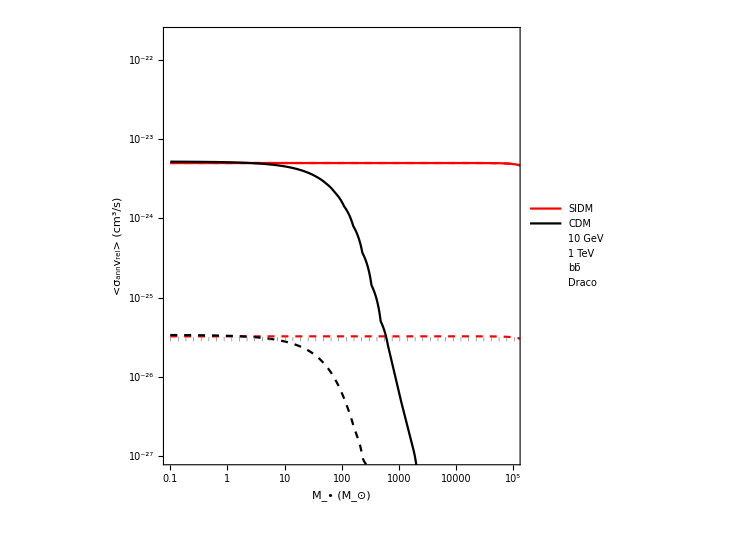

```mathematica
Show[LogLogPlot[ISODracoXsect1000V2alt[x],{x,10^-1,10^10},PlotStyle->{Red},PlotRange->{{10^-1,10^5},{10^-27,  2 10^-22}},PlotLegends-> Placed[LineLegend[{Red,Black},{"SIDM","CDM"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.85,0.85}],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],LogLogPlot[ISODracoXsect10V2alt[x],{x,10^-1,10^11},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{White},{"10 GeV "},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 14]],{0.05,0.34}]],LogLogPlot[ISODracoXsect1000V2alt[x],{x,10^-1,10^11},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{White},{"1 TeV "},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 14]],{0.05,0.77}]],
LogLogPlot[DracoXsect10[x],{x,10^-1,10^10},PlotStyle->{Black,Dashed}],
LogLogPlot[DracoXsect1000[x],{x,10^-1, 10^10},PlotStyle->{Black}],LogLogPlot[3 10^-26,{x,10^-1,10^10},PlotStyle->{Gray,Dotted,Thickness[0.0055]}],LogLogPlot[1,{x,10,10000},PlotStyle->{White},PlotLegends-> Placed[LineLegend[{White},{Text[Style["bb̄",Italic]]
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.85,0.08}]],LogLogPlot[1,{x,10,10000},PlotStyle->{White},PlotLegends-> Placed[LineLegend[{White},{"Draco"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.5,0.93}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.003],Black],FrameLabel-> {Row[{"M_• (",Subscript["M","⊙"],")"}],"<σ_annv_rel> (cm^3/s)"},LabelStyle->Directive[Black,FontSize-> 25],AspectRatio-> 1]
```

```mathematica
stepgamma=(Log10[5/2]-Log10[3/2])/100;
stepgammain= Table[10^x,{x,Log10[3/2],Log10[5/2],stepgamma}];
stepgammainstarr =Table[10^x,{x,Log10[3/2]+5. stepgamma,Log10[5/2],stepgamma}];
stepgammainstar =Table[10^x,{x,Log10[3/2]+1. stepgamma,Log10[5/2],stepgamma}];
```

```mathematica
ISODracoXsectDatagamma= Table[{i,y/.limitISODracostarr[100,10^5,i][[1]]} ,{i,stepgammain}];
ISODracoXsectDatagamma=ReplacePart[ISODracoXsectDatagamma, 1-> {3/2,y/. limitISODraco[100,10^5][[1]]}];
ISODracoXsectgamma=Interpolation[ISODracoXsectDatagamma,InterpolationOrder->1]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction[…]

```mathematica
ISODracoXsectDatagammaV2= Table[{i,y/.limitDracoV2star[100,10^5,i][[1]]} ,{i,stepgammainstar}];
ISODracoXsectDatagammaV2=ReplacePart[ISODracoXsectDatagammaV2, 1-> {3/2,y/. limitISODracoV2[100,10^5][[1]]}];
ISODracoXsectgammaV2=Interpolation[ISODracoXsectDatagammaV2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ISODracoXsectDatagammaV2alt= Table[{i,y/.limitDracoV2staralt[100,10^5,i][[1]]} ,{i,stepgammainstar}];
ISODracoXsectDatagammaV2alt=ReplacePart[ISODracoXsectDatagammaV2alt, 1-> {3/2,y/. limitISODracoV2alt[100,10^5][[1]]}];
ISODracoXsectgammaV2alt=Interpolation[ISODracoXsectDatagammaV2alt,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
DracoXsectDatagamma= Table[{i,y/.limitDraco[100,10^5,i]} ,{i,stepgammainstarr}];
DracoXsectDatagamma=Insert[DracoXsectDatagamma,{3/2,y/.limitDracostarr[100,10^5]},1];
DracoXsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(1. stepgamma),(0.97)y/.limitDracostarr[100,10^5]},2];
DracoXsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(2.stepgamma),(0.94)y/.limitDracostarr[100,10^5]},3];
DracoXsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(3.stepgamma),(0.91)y/.limitDracostarr[100,10^5]},4];
DracoXsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(4.stepgamma),(0.88)y/.limitDracostarr[100,10^5]},5];
DracoXsectgamma=Interpolation[DracoXsectDatagamma,InterpolationOrder->1]
```

$Aborted

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Insert::ins: Cannot insert at position {1} in DracoXsectDatagamma

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Insert[DracoXsectDatagamma,{3/2,2.74152×10^-25},1].

Hold[DracoXsectgamma=Interpolation[DracoXsectDatagamma,InterpolationOrder→1]]

```mathematica
PowerTicks4[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.001]}},{i,min10,max10,3}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]];
```

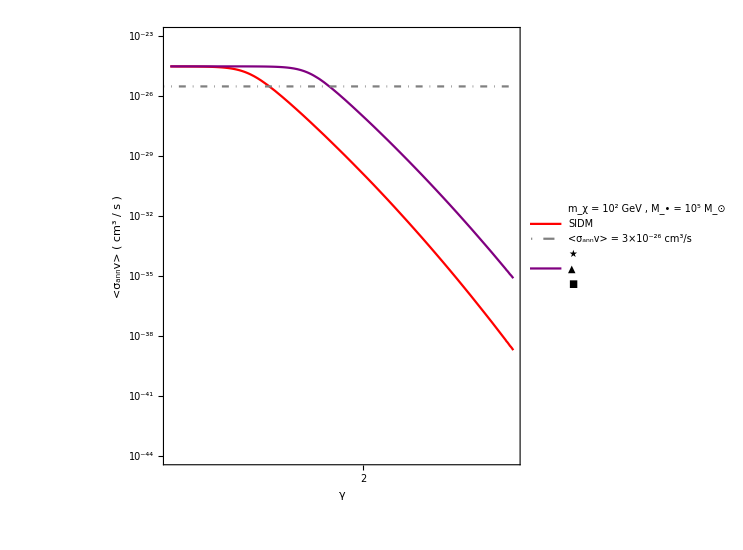

```mathematica
Show[LogLogPlot[ISODracoXsectgammaV2[x],{x,3/2,5/2},PlotRange->{{1.5,2.5},{10^-44,10^-23}},PlotStyle->Red,PlotLegends-> Placed[LineLegend[{White,Red,{Gray ,DotDashed}},{"m_χ = 10^2 GeV , M_• = 10^5 M_⊙ ","SIDM","<σ_annv> = 3×10^-26 cm^3/s"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.35,0.45}],FrameTicks->{{PowerTicks4[True],Automatic},{Automatic,Automatic}}],LogLogPlot[ISODracoXsectgammaV2alt[x],{x,3/2,5/2},PlotStyle->Purple],LogLogPlot[3 10^-26,{x,3/3,5/2},PlotStyle->{Gray,DotDashed},PlotLegends-> Placed[LineLegend[{White},{"★"},LabelStyle->Directive[FontSize-> 17] ],{0.001,0.925}]],LogLogPlot[10^-50,{x,3/3,5/3},PlotStyle->{White,DotDashed},PlotLegends-> Placed[LineLegend[{Purple},{"▲"},LabelStyle->Directive[FontSize-> 17] ],{0.25,0.93}]],LogLogPlot[10^-50,{x,3/3,5/3},PlotStyle->{White,DotDashed},PlotLegends-> Placed[LineLegend[{White},{"■"},LabelStyle->Directive[FontSize-> 17] ],{0.375,0.92}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"γ","<σ_annv> ( cm^3 / s )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```